### Load data and compute the function z = h(τ',τ) and its Taylor series (to demonstrate analyticity is plausible)

```mathematica
ClearAll["Global`*"]

(* Load data *)
wd=SetDirectory@NotebookDirectory[];
pibarData=Import[wd<>"/results_h_function/pibar_exact.dat"];
pibar=Interpolation[pibarData,Method->"Spline"];
pibarprime=Interpolation[Import[wd<>"/results_h_function/pibar_derivative_exact.dat"],Method->"Spline"];
pibar2prime=Interpolation[Import[wd<>"/results_h_function/pibar_2nd_derivative_exact.dat"],Method->"Spline"];
pibar3prime=Interpolation[Import[wd<>"/results_h_function/pibar_3rd_derivative_exact.dat"],Method->"Spline"];
pibar4prime=Interpolation[Import[wd<>"/results_h_function/pibar_4th_derivative_exact.dat"],Method->"Spline"];
tr=Interpolation[Import[wd<>"/results_h_function/tau_r_exact.dat"],Method->"Spline"];
z0func=Interpolation[Import[wd<>"/results_h_function/z_exact.dat"],Method->"Spline"];
t0=pibarData[[1,1]];
tf=pibarData[[-1,1]];

(* first - fifth derivatives of lnT *)
(* derivatives of pibar are computed in the RTA code using finite differences. *)
dlnT[t_]:=(pibar[t] - 4.)/(12.*t);
d2lnT[t_]:=(4. - pibar[t] + t*pibarprime[t])/(12.*t^2);
d3lnT[t_]:=(-8. + 2.*pibar[t] - 2.*t*pibarprime[t] + t^2*pibar2prime[t])/(12.*t^3);
d4lnT[t_]:=(24.-6.*pibar[t]+6.*t*pibarprime[t]-3.*t^2*pibar2prime[t]+t^3*pibar3prime[t])/(12.*t^4);
d5lnT[t_]:=(-96.+24*pibar[t]-24.*t*pibarprime[t]+12.*t^2*pibar2prime[t]-4.*t^3*pibar3prime[t]+t^4*pibar4prime[t])/(12.*t^5);

(* first - fifth derivatives of shear relaxation time *)
dtr[t_]:=-tr[t]*dlnT[t];
d2tr[t_]:=tr[t]*dlnT[t]^2 - tr[t]*d2lnT[t];
d3tr[t_]:=-tr[t]*dlnT[t]^3 + 3.*tr[t]*dlnT[t]*d2lnT[t] - tr[t]*d3lnT[t];
d4tr[t_]:=tr[t]*dlnT[t]^4 - 6.*tr[t]*dlnT[t]^2*d2lnT[t] + 3.*tr[t]*d2lnT[t]^2 + 4.*tr[t]*dlnT[t]*d3lnT[t] - tr[t]*d4lnT[t];
d5tr[t_]:=-tr[t]*dlnT[t]^5 + 10.*tr[t]*dlnT[t]^3*d2lnT[t] - 15.*tr[t]*dlnT[t]*d2lnT[t]^2 +10.*tr[t]*d3lnT[t]*(d2lnT[t]-dlnT[t]^2)+5.*tr[t]*dlnT[t]*d4lnT[t] - tr[t]*d5lnT[t];

(* h(τ',τ) ; s = τ^′*)
h[s_,t_]:=z0func[t]-z0func[s];

(* Taylor series terms h = ∑ Subscript[h, n] (see Eq. (17) *)
(* the 5th-order correction is slightly fluctuating... *)
h0[s_,t_]:=(-(s-t))/tr[t];
h1[s_,t_]:=((s-t)^2*dtr[t])/(2.*tr[t]^2);
h2[s_,t_]:=(-(s-t)^3*(2.*dtr[t]^2-tr[t]*d2tr[t]))/(6.*tr[t]^3);
h3[s_,t_]:=((s-t)^4*(6.*dtr[t]^3-6.*tr[t]*dtr[t]*d2tr[t]+tr[t]^2*d3tr[t]))/(24.*tr[t]^4);
h4[s_,t_]:=(-(s-t)^5*(24.*dtr[t]^4-36.*tr[t]*dtr[t]^2*d2tr[t]+6.*tr[t]^2*d2tr[t]^2+8.*tr[t]^2*dtr[t]*d3tr[t]-tr[t]^3*d4tr[t]))/(120.*tr[t]^5);
h5[s_,t_]:=1/(720.*tr[t]^6)-(s-t)^6*(-120.*dtr[t]^5+240.*tr[t]*dtr[t]^3*d2tr[t]-60.*tr[t]^2*dtr[t]^2*d3tr[t]+10.*tr[t]^2*dtr[t]*(-9.*d2tr[t]^2+tr[t]*d4tr[t])+tr[t]^3*(20.*d2tr[t]*d3tr[t]-tr[t]*d5tr[t]));

H1[s_,t_]:=h0[s,t]+h1[s,t];
H2[s_,t_]:=h0[s,t]+h1[s,t]+h2[s,t];
H3[s_,t_]:=h0[s,t]+h1[s,t]+h2[s,t]+h3[s,t];
H4[s_,t_]:=h0[s,t]+h1[s,t]+h2[s,t]+h3[s,t]+h4[s,t];
H5[s_,t_]:=h0[s,t]+h1[s,t]+h2[s,t]+h3[s,t]+h4[s,t]+h5[s,t];

(* This plot compares exact z = h(τ',τ) (black) to the Taylor expansion Eq. (17) at a given time τ. The convergence, especially at small τ', is plausible *)
hplot = Manipulate[LogLinearPlot[{0,h[s,τ],h0[s,τ],H1[s,τ],H2[s,τ],H3[s,τ],H4[s,τ],H5[s,τ]},{s,0.3,τ},PlotRange->{{0.3,tf-t0},{-1,40}},ImageSize->500,Frame->True,PlotRange->{-1,20},PlotStyle->{Gray,Black,Red,Blue,Green,Purple,Orange,{Red,Dashed}},PlotLabel->Style["z = h(τ',τ)",FontSize->18,Black],FrameLabel->{Style["τ' (fm/c)",FontSize->16,Black]},BaseStyle->{14,Black},FrameStyle->Black],{{τ,tf-t0},0.3,tf-t0,0.01},LabelStyle->Large];

(* Plot L = |Subscript[h, n+1]/Subscript[h, n]| to see if series is converging. It looks like it will stay below unity but it's hard to go to higher orders. *)
(* note: fifth-order correction is fluctuating, probably isn't numerically stable *)
Lplot= Manipulate[LogLinearPlot[{Abs[h1[s,τ]/h0[s,τ]],Abs[h2[s,τ]/h1[s,τ]],Abs[h3[s,τ]/h2[s,τ]],Abs[h4[s,τ]/h3[s,τ]],Abs[h5[s,τ]/h4[s,τ]]},{s,0.3,τ},PlotRange->{{0.3,tf-t0},{0,1}},ImageSize->500,Frame->True,PlotRange->{-1,20},PlotStyle->{Blue,Green,Purple,Orange,{Red,Dashed}},PlotLabel->Style["L = |h_(n + 1)/h_n|",FontSize->18,Black],FrameLabel->{Style["τ' (fm/c)",FontSize->16,Black]},BaseStyle->{14,Black},FrameStyle->Black],{{τ,tf-t0},0.3,tf-t0,0.01},LabelStyle->Large];

Grid[{{hplot,Lplot}}]
Export[wd<>"/h_plot.pdf",hplot];
Export[wd<>"/L_plot.pdf",Lplot];
```

|

### Compare derivatives of Mathematica interpolated relaxation time (black) to my finite difference calculations (green)

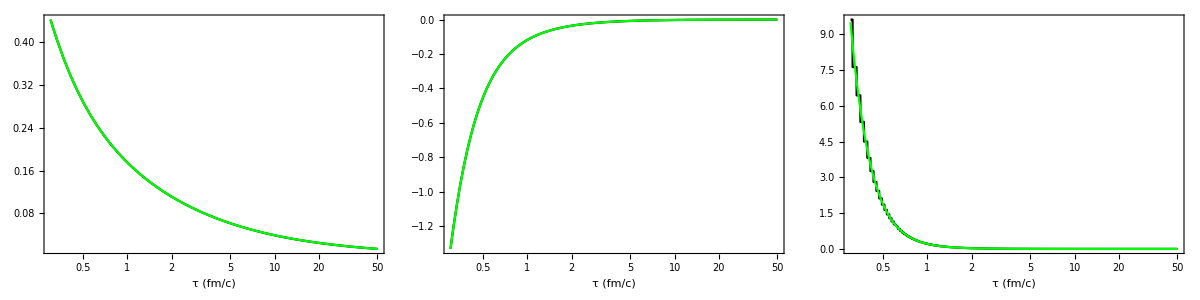

```mathematica
(* Higher-order derivatives of cubic-spline interpolated functions have limitations... *)
(* For example, can't even plot 4th derivative tr''''[t] because it's zero *)
dtrplot=LogLinearPlot[{tr'[t],dtr[t]},{t,0.3,tf-t0},PlotStyle->{Black,Green},PlotRange->All,ImageSize->400,Frame->True,FrameStyle->Black,FrameLabel->{Style["τ (fm/c)",FontSize->16,Black]},BaseStyle->{14,Black},FrameStyle->Black];
d2trplot=LogLinearPlot[{tr''[t],d2tr[t]},{t,0.3,tf-t0},PlotStyle->{Black,Green},PlotRange->All,ImageSize->400,Frame->True,FrameStyle->Black,FrameLabel->{Style["τ (fm/c)",FontSize->16,Black]},BaseStyle->{14,Black},FrameStyle->Black];
d3trplot=LogLinearPlot[{tr'''[t],d3tr[t]},{t,0.3,tf-t0},PlotStyle->{Black,Green},PlotRange->All,ImageSize->400,Frame->True,FrameStyle->Black,FrameLabel->{Style["τ (fm/c)",FontSize->16,Black]},BaseStyle->{14,Black},FrameStyle->Black];
Grid[{{dtrplot,d2trplot,d3trplot}}]
```

### Compare derivatives of interpolated pibar (black) to my finite difference calculations (green)

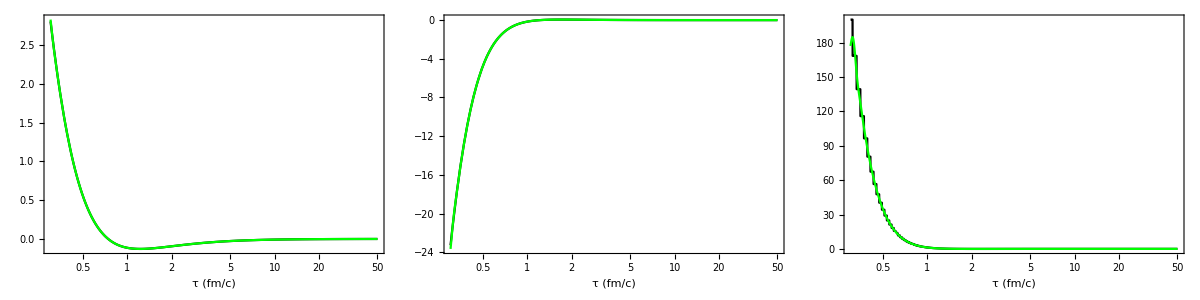

```mathematica
dpibarplot=LogLinearPlot[{pibar'[t],pibarprime[t]},{t,0.3,tf-t0},PlotStyle->{Black,Green},PlotRange->All,ImageSize->400,Frame->True,FrameStyle->Black,FrameLabel->{Style["τ (fm/c)",FontSize->16,Black]},BaseStyle->{14,Black},FrameStyle->Black];
d2pibarplot=LogLinearPlot[{pibar''[t],pibar2prime[t]},{t,0.3,tf-t0},PlotStyle->{Black,Green},PlotRange->All,ImageSize->400,Frame->True,FrameStyle->Black,FrameLabel->{Style["τ (fm/c)",FontSize->16,Black]},BaseStyle->{14,Black},FrameStyle->Black];
d3pibarplot=LogLinearPlot[{pibar'''[t],pibar3prime[t]},{t,0.3,tf-t0},PlotStyle->{Black,Green},PlotRange->All,ImageSize->400,Frame->True,FrameStyle->Black,FrameLabel->{Style["τ (fm/c)",FontSize->16,Black]},BaseStyle->{14,Black},FrameStyle->Black];
Grid[{{dpibarplot,d2pibarplot,d3pibarplot}}]
```

```mathematica
"
```

### Useful formulas

```mathematica
(* derivatives of conservation law *)
D[(f[t]-4)/(12t),{t,1}]//Simplify
D[(f[t]-4)/(12t),{t,2}]//Simplify
D[(f[t]-4)/(12t),{t,3}]//Simplify
D[(f[t]-4)/(12t),{t,4}]//Simplify

(* derivatives of 1/tr[t] *)
D[1/f[t],{t,1}]//Simplify
D[1/f[t],{t,2}]//Simplify
D[1/f[t],{t,3}]//Simplify
D[1/f[t],{t,4}]//Simplify
D[1/f[t],{t,5}]//Simplify
```

(4-f[t]+t f'[t])/(12 t^2)

(-8+2 f[t]-2 t f'[t]+t^2 f''[t])/(12 t^3)

(24-6 f[t]+6 t f'[t]-3 t^2 f''[t]+t^3 f^(3)[t])/(12 t^4)

(-96+24 f[t]-24 t f'[t]+12 t^2 f''[t]-4 t^3 f^(3)[t]+t^4 f^(4)[t])/(12 t^5)

-f'[t]/f[t]^2

(2 f'[t]^2-f[t] f''[t])/f[t]^3

-(6 f'[t]^3-6 f[t] f'[t] f''[t]+f[t]^2 f^(3)[t])/f[t]^4

(24 f'[t]^4-36 f[t] f'[t]^2 f''[t]+6 f[t]^2 f''[t]^2+8 f[t]^2 f'[t] f^(3)[t]-f[t]^3 f^(4)[t])/f[t]^5

(-120 f'[t]^5+240 f[t] f'[t]^3 f''[t]-60 f[t]^2 f'[t]^2 f^(3)[t]+10 f[t]^2 f'[t] (-9 f''[t]^2+f[t] f^(4)[t])+f[t]^3 (20 f''[t] f^(3)[t]-f[t] f^(5)[t]))/f[t]^6